## Rejecting a sine-wave disturbance (Problem 3.21)

```mathematica
Clear["Global`*"];
```

```mathematica
G0 = 1/(1+s);S0=(ω^2+s^2)/(ω+s)^2;K0= G0^-1(S0^-1-1)//Simplify
```

(2 s (1+s) ω)/(s^2+ω^2)

```mathematica
d0=Sin[ω t]  (* disturbance has "correct" frequency *); y0=OutputResponse[TransferFunctionModel[S0,s],d0,t] // Simplify
```

{ⅇ^(-t ω) t ω}

```mathematica
u0=OutputResponse[TransferFunctionModel[-K0 S0,s],d0,t] // Simplify
```

{ⅇ^(-t ω) ω (1+t-t ω)-ω Cos[t ω]-Sin[t ω]}

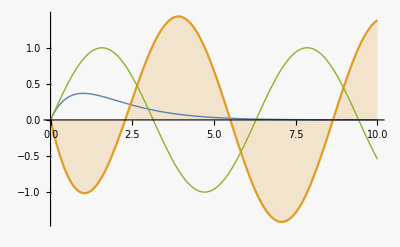

```mathematica
pars0={ω->1};Plot[{y0/.pars0,u0/.pars0,d0/.pars0},{t,0,10},PlotRange->Full,Exclusions->None,Filling->{2->Axis},PlotStyle->{Thick,,Thin}]
```

```mathematica
u0
```

{ⅇ^(-t ω) ω (1+t-t ω)-ω Cos[t ω]-Sin[t ω]}

```mathematica
u0/.pars0
```

{ⅇ^-t-Cos[t]-Sin[t]}

Show that the controller does NOT cancel a disturbance with the wrong frequency.
(You can also just look at the analytic solution.)

```mathematica
d1=Sin[ωd t]   (* disturbance has "wrong" frequency *);
y1 =OutputResponse[TransferFunctionModel[S0,s],d1,t] // Simplify
```

{1/((ω^2+ωd^2)^2)ⅇ^(-t ω) (2 ω ωd (ω^2+t ω^3-ωd^2+t ω ωd^2)-2 ⅇ^(t ω) ω ωd (ω^2-ωd^2) Cos[t ωd]+ⅇ^(t ω) (ω^2-ωd^2)^2 Sin[t ωd])}

```mathematica
Series[y1/.ωd-> ω(1+ϵ),{ϵ,0,1}]
```

{ⅇ^(-t ω) t ω+ⅇ^(-t ω) (-1+ⅇ^(t ω) Cos[t ω]) ϵ+O[ϵ]^2}

```mathematica
u1 = OutputResponse[TransferFunctionModel[-K0 S0,s],d1,t] // Simplify
```

{-1/((ω^2+ωd^2)^2)2 ⅇ^(-t ω) ω ωd (-ω^2-t ω^3+t ω^4+ωd^2-2 ω ωd^2-t ω ωd^2+t ω^2 ωd^2+ⅇ^(t ω) (ω^2-ωd^2+2 ω ωd^2) Cos[t ωd]+ⅇ^(t ω) ωd (2 ω-ω^2+ωd^2) Sin[t ωd])}

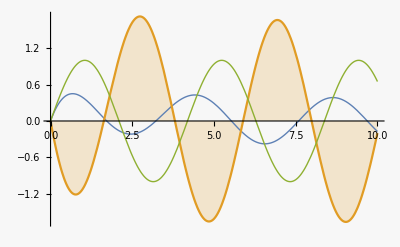

```mathematica
pars1={ω->1,ωd->1.5};
Plot[{y1/.pars1,u1/.pars1,d1/.pars1},{t,0,10},PlotRange->Full,Exclusions->None,Filling->{2->Axis},PlotStyle->{Thick,,Thin}]
```